```mathematica
cells = {{0,0}}
```

{{0,0}}

```mathematica
adds = {{1,0},{0,1},{-1,0},{0,-1}}
```

{{1,0},{0,1},{-1,0},{0,-1}}

```mathematica
NextCells[cells_,adds_:{{1,0},{0,1},{-1,0},{0,-1}}]:=Complement[Union[Catenate[Outer[Plus,cells,adds,1]]],cells]
```

```mathematica
TotalisticPruneQ[{rn_,offsets_},state_,newpos_]:=With[{
rulevec=Reverse[IntegerDigits[rn,2, Length[offsets]]]
},rulevec[[Total[Boole[MemberQ[state,newpos+#]&/@offsets]]]]==1]
```

```mathematica
PlotCells[cells_,opts:OptionsPattern[]]:=ArrayPlot[SparseArray[Thread[cells-Min[cells]+1->1],{Max[cells]-Min[cells]+1,Max[cells]-Min[cells]+1}],opts]
```

```mathematica
PlotCells[cells_,n_Integer,opts:OptionsPattern[]]:=ArrayPlot[SparseArray[Thread[cells+Ceiling[n/2]->1],{n,n}],opts]
```

```mathematica
ArrayPlot[SparseArray[Thread[{{0,0},{1,1}}+Ceiling[10/2]-> 1],{10,10}] // Echo]
```

SparseArray[…]

-Graphics-

```mathematica
NextCells[cells]
```

{{-1,0},{0,-1},{0,1},{1,0}}

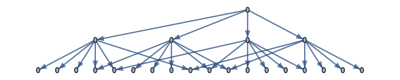

```mathematica
g=NestGraph[Function[s,Union[Append[s,#]]&/@NextCells[s]],{{{0,0}}},2]
```

```mathematica
{{0,1}}
```

```mathematica
Graph[{{1,1},{1,2}},{}]
```

```mathematica
PlotCells[{{0,0},{1,1}},2]
```

-Graphics-

```mathematica
Manipulate[NestGraph[Function[s,Union[Append[s,#]]&/@NextCells[s]],{{{0,0}}},n], {n,0,10, 1}]
```

```mathematica
Manipulate[Graph[NestGraph[Function[s,Union[Append[s,#]]&/@NextCells[s]],{{{0,0}}},n]], {n,0,10, 1}]
```

TotalisticManipulate general method

```mathematica
TotalisticManipulate[rule_: 242, initial_: {{0,0}}, usePlotCells_: False] := Manipulate[
With[{
g = NestGraph[Function[s,If[TotalisticPruneQ[{rule,Tuples[{-1,0,1},2]},s,#], Union[Append[s,#]],Nothing]&/@NextCells[s]],{initial},n]
},
Graph[g,VertexLabels->(#->If[usePlotCells,PlotCells[#,n+4,ImageSize->15],""]&/@VertexList[g]),GraphLayout->"LayeredDigraphEmbedding",AspectRatio->1/2]
],{n,0,10,1}]
```

```mathematica
TotalisticManipulate[242, {{0,0},{1,1},{1,0},{1,-1},{2,-1}}, True]
```

{{0,0},{1,-2},{1,-1},{1,0},{1,1},{2,-1}}

{{0,0},{1,-1},{1,0},{1,1},{2,-2},{2,-1}}

{{0,0},{1,-1},{1,0},{1,1},{2,-1},{2,1}}

{{0,-2},{0,0},{1,-2},{1,-1},{1,0},{1,1},{2,-1}}

{{0,0},{1,-2},{1,-1},{1,0},{1,1},{2,-1},{2,1}}

{{0,0},{1,-1},{1,0},{1,1},{2,-2},{2,-1},{2,1}}

{{0,0},{1,-1},{1,0},{1,1},{2,-2},{2,-1},{3,-2}}

{{0,0},{1,-1},{1,0},{1,1},{2,-2},{2,-1},{3,-1}}

{{0,0},{1,-2},{1,-1},{1,0},{1,1},{2,-1},{2,1}}

{{0,0},{1,-1},{1,0},{1,1},{1,2},{2,-1},{2,1}}

{{0,0},{1,-1},{1,0},{1,1},{2,-2},{2,-1},{2,1}}

{{0,0},{1,-1},{1,0},{1,1},{2,-1},{2,0},{2,1}}

{{0,0},{1,-1},{1,0},{1,1},{2,-1},{2,1},{2,2}}

Introducing canonicalization (for translation):
(convert list of cells to list of cells distanced from minimum coordinates among cells)

```mathematica
CellCanonicalize[state_]:=With[{m=Min/@Transpose[state]},#-m&/@state]
```

```mathematica
CellCanonicalize[{{0,0},{1,-2},{1,-1},{1,0},{1,1},{2,-1}}]
```

```mathematica
TotalisticCanonManipulate[rule_: 242, initial_: {{0,0}}, usePlotCells_: False] := Manipulate[
With[{
g = NestGraph[Function[s,If[TotalisticPruneQ[{rule,Tuples[{-1,0,1},2]},s,#], CellCanonicalize[Union[Append[s,#]]],Nothing]&/@NextCells[s]],{CellCanonicalize[initial]},n]
},
Graph[g,VertexLabels->(#->If[usePlotCells,PlotCells[#,ImageSize->15, Mesh->True],""]&/@VertexList[g]),GraphLayout->"LayeredDigraphEmbedding",AspectRatio->1/2]
],{n,0,10,1}]
```

```mathematica
TotalisticCanonManipulate[242, {{0,0},{1,-1}}, True]
```

```mathematica
TotalisticCanonManipulate[242, {{0,0},{-1,1},{0,1},{1,1}}, True]
```

Now with rotational canonicalization

```mathematica
CellCanonicalizeRotations[cells_]:=Module[{dim,mins,positive,array,canonarray},dim=Max[#]-Min[#]+1&/@Transpose[cells];
mins=Min/@Transpose[cells];
positive=#-mins+1&/@cells;
array=ReplacePart[ConstantArray[0,dim],positive->1];
canonarray=First[Sort[ResourceFunction["ArrayRotations"][ResourceFunction["ArrayCrop"][array]]]];
Position[canonarray,1]-1]
```

```mathematica
TotalisticFullCanonManipulate[rule_: 242, initial_: {{0,0}}, usePlotCells_: False] := Manipulate[
With[{
g = NestGraph[Function[s,If[TotalisticPruneQ[{rule,Tuples[{-1,0,1},2]},s,#], CellCanonicalizeRotations[Union[Append[s,#]]],Nothing]&/@NextCells[s]],{CellCanonicalizeRotations[initial]},n]
},
Graph[g,VertexLabels->(#->If[usePlotCells,PlotCells[#,ImageSize->15, Mesh->True],""]&/@VertexList[g]),GraphLayout->"LayeredDigraphEmbedding",AspectRatio->1/2]
],{n,0,10,1}]
```

```mathematica
TotalisticFullCanonManipulate[242, {{0,0},{1,-1}}, True]
```

```mathematica
TotalisticFullCanonManipulate[242, {{0,0},{0,1}}, True]
```

Halt find

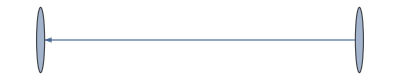

```mathematica
g2 = NestGraph[Function[s,If[TotalisticPruneQ[{242,Tuples[{-1,0,1},2]},s,#], CellCanonicalizeRotations[Union[Append[s,#]]],Nothing]&/@NextCells[s]],{CellCanonicalizeRotations[{{0,0},{1,1}}]},1]
```

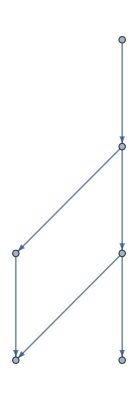

```mathematica
NestGraph[Function[s,If[TotalisticPruneQ[{242,Tuples[{-1,0,1},2]},s,#], CellCanonicalizeRotations[Union[Append[s,#]]],Nothing]&/@NextCells[s]],%,1]
```

```mathematica
HaltFind[rule_: 242, initial_: {{0,0}}] := NestWhile[Function[s,If[TotalisticPruneQ[{rule,Tuples[{-1,0,1},2]},s,#], Union[Append[s,#]],Null]&/@NextCells[CellCanonicalizeRotations[s]]], initial, MemberQ[]&, 1, 2
]
```

```mathematica
HaltFind[242, {{0,0},{-1,1}}]
```

{{0,0},{-1,1}}

```mathematica
SelectFirst[{0,Nothing} // Echo,#==0&]
```

{0}

0